```mathematica
Needs["OpenCLLink`"]
```

```mathematica
tpl="
#define Eps ( sqrt(delta12 + px*px + py*py - sqrt(delta24 + delta32*(px*px + py*py))) )
#define rDEps ( fabs(2*sqrt(delta12 + p2r - sqrt(delta24 + delta32*p2r))/(1 - 0.5f*delta32/sqrt(delta24 + delta32*p2r))) )
#define Vx ( px*(1 - 0.5f*delta32/sqrt(delta24 + delta32*(px*px + py*py)))/sqrt(delta12 + px*px + py*py - sqrt(delta24 + delta32*(px*px + py*py))) )
#define Vy ( py*(1 - 0.5f*delta32/sqrt(delta24 + delta32*(px*px + py*py)))/sqrt(delta12 + px*px + py*py - sqrt(delta24 + delta32*(px*px + py*py))) )
#define Fx ( Exc + Ex*cos(wx*t) + H*vy )
#define Fy ( Eyc + Ey*cos(wy*t - phi) - H*vx )
#define Value ( vx*Ex*cos(wx*t) + vy*Ey*cos(wy*t + phi) )

#define pi ( 3.14159265f )
#define RNGInit unsigned int x1, y1, z1, w1; x1 = seed[idx]; y1 = 362436069; z1 = 521288629; w1 = 88675123
#define rand_uniform random_uniform(&x1, &y1, &z1, &w1)

float random_uniform(unsigned int * x1,
				unsigned int * y1,
				unsigned int * z1,
				unsigned int * w1){
	unsigned int t1 = ((*x1)^((*x1)<<11));
	(*x1) = (*y1);
	(*y1) = (*z1);
	(*z1) = (*w1); 
	(*w1) = ((*w1)^((*w1)>>19))^(t1^(t1>>8)); 
	return ((float)(*w1))/(UINT_MAX);
}

__kernel void RNGtest(__global float * mas, __global int * seed){
    int idx = get_global_id(0);
    RNGInit;
    mas[idx] = rand_uniform;
}

__kernel void jobKernel (__global float * dev_average_value_array, __global int * num_cols, __global float * dev_params, __global int * seed )
{ 
	// Thread index
	int idx = get_global_id(0);

	// RGN initialization
	RNGInit;
    // Copying parameters in local variables (for speed)
    float Exc = dev_params[0];
    float Eyc = dev_params[1];
    float Ex = dev_params[2];
    float Ey = dev_params[3];
    float H = dev_params[4];
    float wx = dev_params[5];
    float wy = dev_params[6];
    float phi = dev_params[7];
    float wla_max = dev_params[8];
    float wlo_max = dev_params[9];
    float w0 = dev_params[10];
    float delta1 = dev_params[11];
    float delta2 = dev_params[12];
    float delta3 = dev_params[13];
    float all_time = dev_params[14];
    float dt = dev_params[15];

    // Prepare variables and work
    float px = 0.0f;
    float py = 0.0f;
    float vx = 0.0f;
    float vy = 0.0f;
    float value = 0.0f;
    float temp = 0.0f;
    int numcols = 0;
    float p = -log(rand_uniform);
    float psi = 2*pi*rand_uniform;
    px = p*cos(psi);
    py = p*sin(psi);
    float t = 0.0f;
    float wsum = 0.0f;
    float r1 = 0.0f;
    float r2 = 0.0f;
    float w[] = {0.0f, 0.0f, 0.0f, 0.0f};
    float r = - log(rand_uniform);
    float beta = 0.0f;
    float p2r = 0.0f;
    float eps = 0.0f;
    float delta24 = delta2*delta2*delta2*delta2;
    float delta34 = delta3*delta3*delta3*delta3;
    float delta32 = delta3*delta3;
    float delta12 = delta1*delta1;
    int i;

    while( t < all_time ){
		vx = Vx;
		vy = Vy;
		value += Value*dt;
		px += Fx*dt;
		py += Fy*dt;
		eps = Eps;
        t += dt;

        // Scattering
        p2r = px*px + py*py;
		w[0] = 0.5f*wla_max*rDEps;
		w[1] = 0.0f;
		p2r = delta32 + (px*px + py*py) - 2*sqrt(delta24 + delta32*(px*px + py*py));
		if(p2r > 0)
			w[1] = 0.5f*wla_max*rDEps;
		w[2] = 0.0f;
		p2r = 0.0f;
		temp = 4*delta24 - 4*delta12*delta32 + delta34 + 4*delta32*(eps-w0)*(eps-w0);
		if(temp >= 0)
			p2r = 0.5f*(-2*delta12 + delta32 + 2*(eps-w0)*(eps-w0) + sqrt(temp));
		if(p2r > 0)
			w[2] = 0.5f*wlo_max*rDEps;
		w[3] = 0.0f;
		if(temp >= 0)
			p2r = 0.5f*(-2*delta12 + delta32 + 2*(eps-w0)*(eps-w0) - sqrt(temp));
		if(p2r > 0)
			w[3] = 0.5f*wlo_max*rDEps;
		wsum += (w[0] + w[1] + w[2] + w[3])*dt;
		if(wsum > r){
			wsum = 0.0f;
			numcols += 1;
			r = rand_uniform;
			psi = atan2(py, px);
			temp = w[0];
			i = 0;
			while(temp < r*(w[0] + w[1] + w[2] + w[3])){
				i += 1;
				temp += w[i];
            };
			if ( i == 0 ){
				p = sqrt(px*px + py*py);
			};
			if ( i == 1 ){
				p2r = delta32 + (px*px + py*py) - 2*sqrt(delta24 + delta32*(px*px + py*py));
				p = sqrt(p2r);
			};
			if ( i == 2 ){
				eps = eps - w0;
				temp = 4*delta24 - 4*delta12*delta32 + delta34 + 4*delta32*eps*eps;
				p2r = 0.5f*(-2*delta12 + delta32 + 2*eps*eps + sqrt(temp));
				p = sqrt(p2r);
			};
			if ( i == 3 ){
				eps = eps - w0;
				temp = 4*delta24 - 4*delta12*delta32 + delta34 + 4*delta32*eps*eps;
				p2r = 0.5f*(-2*delta12 + delta32 + 2*eps*eps - sqrt(temp));
				p = sqrt(p2r);
			};
			do{
				r1 = 2*pi*rand_uniform;
				r2 = rand_uniform;
			} while(0.5f*(1+cos(r1)) < r2);
			px = p*cos(psi + r1);
			py = p*sin(psi + r1);
			r = - log(rand_uniform);
			};
		};
        value /= t;
        dev_average_value_array [idx] = value;
        num_cols[idx] = numcols;
    }
";
```

```mathematica
fun1=OpenCLFunctionLoad[tpl,"RNGtest",{{"Float","Output"},{"Integer32","Input"}},100,"ShellOutputFunction"->None];
values=ConstantArray[0,500];
seeds=RandomInteger[{362436000,562436000},500];
Mean[fun1[values,seeds][[1]]]
StandardDeviation[fun1[values,seeds][[1]]]
```

0.50375

0.288623

```mathematica
n = 100;
fun=OpenCLFunctionLoad[tpl,"jobKernel",{{"Float","Output"},{"Integer32","Output"},{"Float","Input"},{"Integer32","Input"}},n];
values=Table[0,{i,n}];
numcols=Table[0,{i,n}];
params=Table[0,{i,16}];
```

```mathematica
outmas={};
VarName="H";
IterMessage="Solve is run!";
Dynamic[IterMessage]
gb=AbsoluteTime[];
For[var=0,var≤800,var+=20,
b=AbsoluteTime[];
(* Dimension units*)
EvToErg=1.6*10^-12;
k=1.38*10^-16 ;(*Boltzmann constant*)
c=3*10^10; (*Speed of light*)
T=200 ;(*Temperature*)
Dak=18*EvToErg;(* Acoustic phonon constant*)
Dopt=1.4*10^9*EvToErg; (*Optic phonon constant*)
h=10^-27 ;(* Dirak constant*)
ro=2*7.7*10^-8 ;(* Surface dens*)
vs=2.6*10^6 ;(* Speed of sound*)
el=4.8*10^-10 ;(* Electron charge*)
vf=10^8 ;(* Speed of Fermi*)
n0=10^12; (* 2D concentration*)
w0=0.196*EvToErg/h;(* Optic phonon limit frequency*)
eperp=0.35*EvToErg;
     U=0.1*EvToErg; 
     delta1=Sqrt[eperp*eperp/2+U*U];
     delta2=eperp/Sqrt[2];
     delta3=Sqrt[eperp*eperp+4*U*U];
nuac=(k*T*Dak)^2/(2*h^3*ro*vs^2*vf^2);
nuopt=k*T*Dopt^2/(4*h^2*ro*w0*vf^2);
HSGS=k*T*nuac*c/el/vf^2;
HSI=HSGS/10000.0;
ESGS=k*T*nuac/el/vf;
ESI=ESGS*300.0;
jSGS=n0*vf*el;
powerSGS=jSGS*ESGS;
power0Etau=n0*el^2*vf^2/eperp;
(*Parameters*)
params[[1]]=0;(*Exc*)
params[[2]]=0;(*Eyc*)
params[[3]]=0.1/ESGS;(*Ex*)
params[[4]]=0.1/ESGS;(*Ey*)
params[[5]]=var;(*H*)
params[[6]]=20;(*wx*)
params[[7]]=20;(*wy*)
params[[8]]=Pi/6;(*phi*)
params[[9]]=1;(*wla_max*)
params[[10]]=nuopt/nuac;(*wlo_max*)
params[[11]]=h*w0/k/T;(*w0*)
params[[12]]=delta1/k/T;(*delta1*)
params[[13]]=delta2/k/T;(*delta2*)
params[[14]]=delta3/k/T;(*delta3*)
params[[15]]=100;(*all_time*)
params[[16]]=0.001;(*step_time*)
(*Solve*)
count=10;
out={};
Do[
res={Indeterminate};
While[Length[Position[res,Indeterminate]]>0,
seeds=RandomInteger[{100000000,1000000000},n];
res=fun[values,numcols,params,seeds];
];
AppendTo[out,res];
,{k,count}
];
res=Mean[out];
tau=params[[15]]/Mean[res[[2]]]/nuac;
power0=power0Etau*tau*(params[[3]]*ESGS)^2;
H=params[4]*HSGS;
Omega=2*el*vf^2*H/c/eperp;
AppendTo[outmas,{var,Mean[res[[1]]]*powerSGS/power0,StandardDeviation[res[[1]]]*powerSGS/power0,U/eperp,eperp/k/T,Omega,tau,(params[[6]]+params[[7]])/2*nuac}];
e=AbsoluteTime[];
IterMessage=VarName<>" = "<>ToString[N[var]]<>" solve for "<>ToString[e-b]<>" second(s)";
];
ge=AbsoluteTime[];
IterMessage="Solve is over for "<>ToString[ge-gb]<>" second(s)";
```

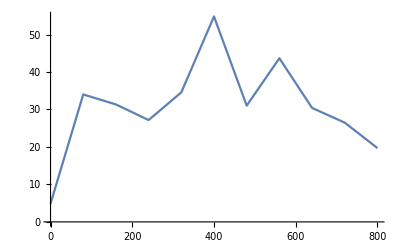

```mathematica
ListPlot[{outmas[[1;;All;;1,1;;2]]},Joined->True,InterpolationOrder->1,PlotRange->All]
```

```mathematica
outmas1=outmas;
```

```mathematica
outmas2=outmas;
```

```mathematica
outmas3=outmas;
```

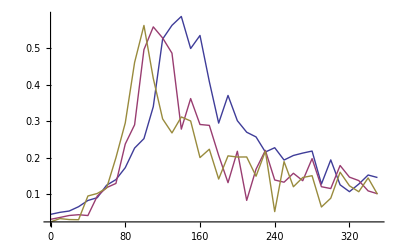

```mathematica
outmas1=Select[outmas1,NumberQ[#[[2]]]&];
outmas2=Select[outmas2,NumberQ[#[[2]]]&];
outmas3=Select[outmas3,NumberQ[#[[2]]]&];
ListPlot[{outmas1[[1;;All;;1,1;;2]],outmas2[[1;;All;;1,1;;2]],outmas3[[1;;All;;1,1;;2]]},Joined->True,InterpolationOrder->1,PlotRange->All]
```

```mathematica
FindHalfWith[mas_]:=Module[{fun,max,lh,rh},
fun=Interpolation[mas];
max=First[NMaximize[{fun[x],x>Min[mas[[All,1]]]&&x<Max[mas[[All,1]]]},x]];
lh=x/.FindRoot[fun[x]-max/Sqrt[2]==0,{x,Min[mas[[All,1]]],Min[mas[[All,1]]],Max[mas[[All,1]]]}];
rh=x/.FindRoot[fun[x]-max/Sqrt[2]==0,{x,Max[mas[[All,1]]],Min[mas[[All,1]]],Max[mas[[All,1]]]}];
Return[{max,rh-lh}]
]
```